# 3-local Ising Optimisation using Simulated Annealing

```mathematica
TestHamiltonian=RandomHamiltonian[5,0,0];
```

```mathematica
Timing[Minimize[{TestHamiltonian,Constraints[11]},SpinVariables[11]]]
```

{33.8877,{-31.6153,{s1→-1.,s2→-1.,s3→-1.,s4→1.,s5→-1.,s6→1.,s7→1.,s8→-1.,s9→1.,s10→-1.,s11→1.}}}

```mathematica
Timing[NMinimize[{TestHamiltonian,Constraints[5]} ,SpinVariables[5],Method-> "SimulatedAnnealing"]]
```

{0.078368,{-4.27714,{s1→1.,s2→-1.,s3→1.,s4→1.,s5→-1.}}}

### Constraint generating function

```mathematica
(*Generate arbitrary constraints for n spins saying that each one must either be +1 or -1*)
Constraint[index_]:="(s"<>ToString[index] <>"==1||s"<>ToString[index]<>"==-1)&&"
Constraints[spins_]:=ToExpression[StringDrop[StringJoin[Array[Constraint,spins]],-2]]
```

```mathematica
(*Example*)
Constraints[5]
```

(s1==1||s1==-1)&&(s2==1||s2==-1)&&(s3==1||s3==-1)&&(s4==1||s4==-1)&&(s5==1||s5==-1)

### Arbitrary 3-local Hamiltonian generating function

```mathematica
(*Useful function to generate si Mathematica expression*)
Spin[index_]:=ToExpression["s"<>ToString[index]]
```

```mathematica
(*Generate a set of random local fields. The sparseness parameter controls the probability of a local field being zero*)
```

```mathematica
LocalField[spin_,sparseness_]:=If[RandomReal[]>sparseness,RandomReal[{-1,1},WorkingPrecision->3]*Spin[spin],0]
LocalFields[spins_,sparseness_]:=Sum[LocalField[i,sparseness],{i,1,spins}]
```

```mathematica
(*Example*)
LocalFields[10,0]
```

0.561 s1+0.158 s10+0.928 s2-0.219 s3-0.719 s4-0.459 s5-0.557 s6+0.641 s7-0.0801 s8-0.709 s9

```mathematica
(*Functions to generate a random set of coupling terms for n spins. The sparseness parameter controls the probability of a coupling being zero*)
```

```mathematica
CouplingTerm[i_,combinations_,sparseness_]:=If[RandomReal[]>sparseness,RandomReal[{-1,1}]*combinations[[i]][[1]]*combinations[[i]][[2]]*combinations[[i]][[3]],0]
CouplingTerms[spins_,sparseness_]:=Module[{combinations},combinations=Subsets[Array[Spin,spins],{3}];Sum[CouplingTerm[i,combinations,sparseness],{i,1,Binomial[spins,3]}]]
```

```mathematica
(*Example*)
CouplingTerms[6,0]
```

-0.0100929 s1 s2 s3-0.291353 s1 s2 s4-0.405305 s1 s3 s4-0.449909 s2 s3 s4-0.835188 s1 s2 s5+0.635722 s1 s3 s5-0.805897 s2 s3 s5-0.917595 s1 s4 s5+0.612925 s2 s4 s5+0.931654 s3 s4 s5-0.761988 s1 s2 s6-0.349229 s1 s3 s6+0.172708 s2 s3 s6+0.534493 s1 s4 s6-0.996628 s2 s4 s6-0.840386 s3 s4 s6+0.774414 s1 s5 s6+0.45895 s2 s5 s6+0.722741 s3 s5 s6+0.962097 s4 s5 s6

```mathematica
(*Combine the above functions into one which generates an arbitrary Hamiltonian for n spins. The sparseness parameters control the probability of a local field or coupling being zero*)
RandomHamiltonian[spins_,localSparseness_,couplingSparseness_]:=LocalFields[spins,localSparseness]+CouplingTerms[spins,couplingSparseness]
```

```mathematica
RandomHamiltonian[3,0,0]
```

0.375 s1-0.676 s2-0.42 s3-0.240356 s1 s2 s3

### Spin Variable Generating Function

```mathematica
SpinVariables[spins_]:=Array[Spin,spins]
```

```mathematica
SpinVariables[10]
```

{s1,s2,s3,s4,s5,s6,s7,s8,s9,s10}

### Turn our (classical) Hamiltonian function into a matrix

```mathematica
(*Function to turn the generated local fields into a matrix*)
LocalFieldMatrix[hamiltonianF_,spins_,spin_]:=Module[{matrix,list,h},{list=List@@hamiltonianF,If[StringTake[ToString[list[[spin]]],1]=="-",h=ToExpression[StringTake[ToString[list[[spin]]],6]],h=ToExpression[StringTake[ToString[list[[spin]]],5]]],If[spin==1,matrix=h*pauliZ,matrix=IdentityMatrix[2]]};{Do[If[spin==i,matrix=KroneckerProduct[matrix,h*pauliZ],matrix=KroneckerProduct[matrix,IdentityMatrix[2]]],{i,2,spins}],matrix}]
LocalFieldsMatrix[hamiltonianF_,spins_]:=Sum[FunctionToMatrix[hamiltonianF,spins,i][[2]],{i,1,spins}]
```

```mathematica
(*Example*)
Fields=LocalFields[3,0]
LocalFieldsMatrix[Fields,3]//MatrixForm
```

0.727 s1-0.195 s2+0.826 s3

(1.358 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.294 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1.748 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.096 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.096 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -1.748 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.294 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -1.358)

### Test timing of Minimize and NMinimize

```mathematica
TestHamiltonian=RandomHamiltonian[5,0,0]
(*Minimize solves the problem exactly*)
Minimize[{TestHamiltonian,Constraints[5]},SpinVariables[5]]
(*NMinimize attempts to solve the problem with some probabilistic algorithm, in this case Simulated Annealing*)
NMinimize[{TestHamiltonian,Constraints[5]} ,SpinVariables[5],Method-> "SimulatedAnnealing"]
```

{-6.51797,{s1→1.,s2→-1.,s3→1.,s4→-1.,s5→1.}}

{-6.51797,{s1→1.,s2→-1.,s3→1.,s4→-1.,s5→1.}}

```mathematica
timesExact={};
solnsExact={};
energiesExact={};
timesAnneal={};
solnsAnneal={};
energiesAnneal={};
Do[Module[{testHamiltonian,tempTimeExact,tempTimeAnneal,tempSolnExact,tempSolnAnneal,tempEnergyExact,tempEnergyAnneal},testHamiltonian=RandomHamiltonian[i,0,0]; {{tempTimeExact,{tempEnergyExact,tempSolnExact}}=Timing[Minimize[{testHamiltonian,Constraints[i]},SpinVariables[i]]],{tempTimeAnneal,{tempEnergyAnneal,tempSolnAnneal}}=Timing[NMinimize[{testHamiltonian,Constraints[i]},SpinVariables[i]]],timesExact=Append[timesExact,{i,tempTimeExact}],timesAnneal=Append[timesAnneal,{i,tempTimeAnneal}],solnsExact=Append[solnsExact,{i,tempSolnExact}],solnsAnneal=Append[solnsAnneal,{i,tempSolnAnneal}],energiesExact=Append[energiesExact,{i,tempEnergyExact}],energiesAnneal=Append[energiesAnneal,{i,tempEnergyAnneal}],Print[ToString[i]<>" Spin Run Complete"]}],{i,3,12}]
```

3 Spin Run Complete

4 Spin Run Complete

5 Spin Run Complete

6 Spin Run Complete

7 Spin Run Complete

8 Spin Run Complete

9 Spin Run Complete

10 Spin Run Complete

11 Spin Run Complete

12 Spin Run Complete

```mathematica
timesExact
solnsExact
energiesExact
```

{{3,0.043038},{4,0.055877},{5,0.087378},{6,0.196667},{7,0.444824},{8,1.02775},{9,2.95132},{10,10.6649},{11,34.3471},{12,133.617}}

{{3,{s1→1.,s2→1.,s3→-1.}},{4,{s1→1.,s2→-1.,s3→1.,s4→1.}},{5,{s1→1.,s2→1.,s3→1.,s4→1.,s5→-1.}},{6,{s1→-1.,s2→1.,s3→1.,s4→1.,s5→1.,s6→-1.}},{7,{s1→-1.,s2→-1.,s3→1.,s4→1.,s5→-1.,s6→1.,s7→-1.}},{8,{s1→1.,s2→1.,s3→1.,s4→-1.,s5→-1.,s6→1.,s7→1.,s8→1.}},{9,{s1→-1.,s2→1.,s3→-1.,s4→1.,s5→1.,s6→1.,s7→1.,s8→-1.,s9→-1.}},{10,{s1→1.,s2→1.,s3→1.,s4→1.,s5→1.,s6→-1.,s7→-1.,s8→-1.,s9→-1.,s10→-1.}},{11,{s1→1.,s2→-1.,s3→-1.,s4→1.,s5→1.,s6→-1.,s7→-1.,s8→-1.,s9→-1.,s10→-1.,s11→1.}},{12,{s1→-1.,s2→1.,s3→-1.,s4→1.,s5→-1.,s6→-1.,s7→-1.,s8→1.,s9→-1.,s10→-1.,s11→-1.,s12→-1.}}}

{{3,-2.15167},{4,-3.13931},{5,-3.0113},{6,-6.74845},{7,-8.61251},{8,-13.4825},{9,-19.0233},{10,-21.9294},{11,-37.631},{12,-34.1316}}

```mathematica
timesAnneal
solnsAnneal
energiesAnneal
```

{{3,0.016974},{4,0.041436},{5,0.073923},{6,0.196814},{7,0.403067},{8,1.03856},{9,2.95686},{10,10.1655},{11,36.6207},{12,138.037}}

{{3,{s1→1.,s2→1.,s3→-1.}},{4,{s1→1.,s2→-1.,s3→1.,s4→1.}},{5,{s1→1.,s2→1.,s3→1.,s4→1.,s5→-1.}},{6,{s1→-1.,s2→1.,s3→1.,s4→1.,s5→1.,s6→-1.}},{7,{s1→-1.,s2→-1.,s3→1.,s4→1.,s5→-1.,s6→1.,s7→-1.}},{8,{s1→1.,s2→1.,s3→1.,s4→-1.,s5→-1.,s6→1.,s7→1.,s8→1.}},{9,{s1→-1.,s2→1.,s3→-1.,s4→1.,s5→1.,s6→1.,s7→1.,s8→-1.,s9→-1.}},{10,{s1→1.,s2→1.,s3→1.,s4→1.,s5→1.,s6→-1.,s7→-1.,s8→-1.,s9→-1.,s10→-1.}},{11,{s1→1.,s2→-1.,s3→-1.,s4→1.,s5→1.,s6→-1.,s7→-1.,s8→-1.,s9→-1.,s10→-1.,s11→1.}},{12,{s1→-1.,s2→1.,s3→-1.,s4→1.,s5→-1.,s6→-1.,s7→-1.,s8→1.,s9→-1.,s10→-1.,s11→-1.,s12→-1.}}}

{{3,-2.15167},{4,-3.13931},{5,-3.0113},{6,-6.74845},{7,-8.61251},{8,-13.4825},{9,-19.0233},{10,-21.9294},{11,-37.631},{12,-34.1316}}

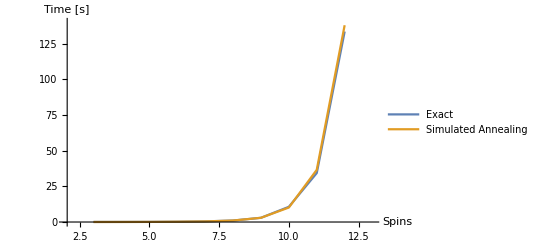

```mathematica
ListLinePlot[{timesExact,timesAnneal},PlotRange->{{2,13},{0,140}},AxesLabel->{"Spins","Time [s]"},PlotLegends->{"Exact","Simulated Annealing"}]
```

### Test Simulated Annealing on Large Problem Sizes

```mathematica
times = {};
energies={};
solns={};
Do[Module[{testHamiltonian,tempTime,tempSoln,tempEnergy},testHamiltonian=RandomHamiltonian[i,0,0]; {{tempTime,{tempEnergy,tempSoln}}=Timing[NMinimize[{testHamiltonian,Constraints[i]},SpinVariables[i]]],times=Append[times,{i,tempTime}],solns=Append[solns,{i,tempSoln}],energies=Append[energies,{i,tempEnergy}],Print[ToString[i]<>" Spin Run Complete"]}],{i,15,15}]
```

3 Spin Run Complete

4 Spin Run Complete

5 Spin Run Complete

```mathematica
times
energies
solns
```

{{3,0.015812},{4,0.035957},{5,0.074337}}

{{3,-2.50256},{4,-2.16075},{5,-4.315}}

{{3,{s1→-1.,s2→-1.,s3→-1.}},{4,{s1→1.,s2→1.,s3→-1.,s4→1.}},{5,{s1→1.,s2→1.,s3→-1.,s4→-1.,s5→1.}}}